# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y,ξunit, Nf, Nr];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[0.9,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Polytope

Formulas deduction
Base Contraints Fuctions...
Nf * vg + vl - v0 = 0; (1)
Nf * vg + Nr * v0 = vatp; (2)
vg <= Min{Vg, cg * D/X} = Mg; (3)
vl <= 0 <= v0 <= R; (4)

----- v0 ------
Just clean v0 from (2).
v0 = (vatp - Nf * vg)/Nr; (5)

----- vl -------
Clear vl from (1)
vl = v0 - Nf * vg
Using (5)
vl = (vatp - Nf * vg)/Nr - Nf * vg
vl = (vatp - Nf * vg - Nf * vg * Nr)/Nr
vl = (vatp - Nf * vg (1 + Nr))/Nr; (6)

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(Nf+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vertices[ξ_]:=If[vatpMaxGlobal[ξ]>19R,
{{0,0},{2vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},{20R,R/2}},
{{0,0},{2vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}]

polytope[ξ_][vg_,vatp_]:=Boole[vatp/(Nf(1+Nr))≤vg≤vgMaxGlobal[ξ]∧Nf vg ≤ vatp ≤ Nr R + Nf vg];
```

```mathematica
Print["Max glucose uptake -> ",vgMaxGlobal[2]];
Print["Lactate uptake -> ",vl[2,2]];
Print["Respiration Rate -> ",vo[2,2]];
Print["Min glucose uptake -> ",vgMinLocal[2]];
Print["Max glucose uptake -> ",vgMaxLocal[2][2]];
Print["Max atp Rate -> ",vatpMaxGlobal[2]];
```

Max glucose uptake -> 1/2

Lactate uptake -> -78/19

Respiration Rate -> -2/19

Min glucose uptake -> 1/21

Max glucose uptake -> 1/2

Max atp Rate -> 43/5

Growth Functions

```mathematica
ClearAll[δ,λ,λmax]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpMaxGlobal[ξ]]
```

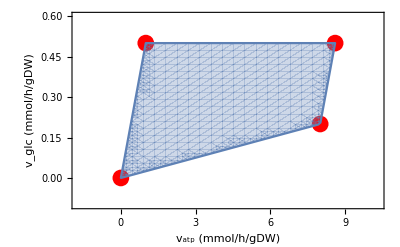

```mathematica
Module[{ξ=2},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2 vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]}]]]
```

Partition, expected values, variances, covariances

```mathematica
ClearAll[generateIntegral];

(* The integral in all the polytope *) 
generateIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
int1=Simplify@Integrate[Exp[-β y(vatpMaxGlobal[ξ]-vatp)]fun[vg,vatp],
{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
Piecewise[{{0, atplb≥atpub}, {int1, β>0}, {int0, β==0}}]];
```